LevelScheme examples: Plots

M. A. Caprio, Department of Physics, University of Notre Dame

## Package initialization

If you have not already loaded the LevelScheme package since starting this Mathematica session, you must do so now.  See the user guide for information first on installing the package and then on loading it at the beginning of each Mathematica session.

```mathematica
Get["LevelScheme`"];
```

## Plot and inset plot -- Bessel functions

In this example, the graphical output of Plot is directly included in the figure, using RawGraphics.

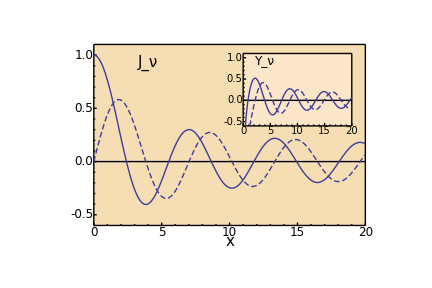

```mathematica
Figure[
{

(* main panel *)
FigurePanel[
{{0,1},{0,1}},
PlotRange->{{0,20},{-0.6,1.1}},
FrameTicks->{LinTicks[0,20],LinTicks[-1,1,0.5,5]},
FontSize->15,LabB->textit["x"],BufferB->2.5,
TickFontSize->12,
Background->Wheat
],
SchemeLine[{{0,0},{20,0}}],
ScaledLabel[{0.2,0.9},SubscriptBox[textit["J"],"ν"],FontSize->15],
RawGraphics[Plot[BesselJ[0,x],{x,0,20}]],
RawGraphics[Plot[BesselJ[1,x],{x,0,20}],Dashing->Automatic],

(* inset panel *)
ScaledFigurePanel[
{{0.55,0.95},{0.55,0.95}},
PlotRange->{{0,20},{-0.6,1.1}},
FrameTicks->{LinTicks[0,20],LinTicks[-1,1,0.5,5]},
TickFontSize->10,
Background->Eggshell
],
SchemeLine[{{0,0},{20,0}}],
ScaledLabel[{0.2,0.9},SubscriptBox[textit["Y"],"ν"],FontSize->12],
RawGraphics[Plot[BesselY[0,x],{x,0,20}]],
RawGraphics[Plot[BesselY[1,x],{x,0,20}],Dashing->Automatic]

},
PlotRange->{{-0.2,1.1},{-0.2,1.1}},ImageSize->72*{6,4}
]
```

## Multipanel plot -- Lissajous curves

This plot illustrates the use of different sized panels, gaps between panels, and custom tick marks.
In this example, the graphical output of Plot or ParametricPlot is directly included in the figure, using RawGraphics.

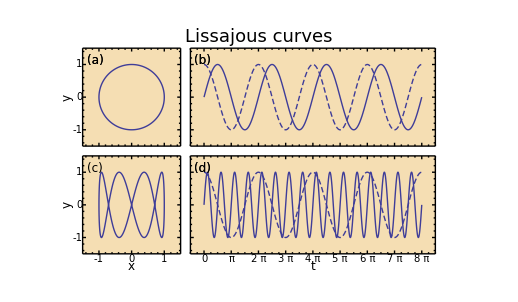

```mathematica
Figure[
{

ScaledLabel[{0.5,1},"Lissajous curves",FontSize->18,Offset->{0,1}],

Multipanel[
{{0,1},{0,1}},
{2,2},
XPlotRanges->{{-1.5,1.5},{-Pi/2,8*Pi+Pi/2}},
YPlotRanges->{-1.5,1.5},
XFrameLabels->{textit["x"],textit["t"]},BufferB->2.5,
YFrameLabels->textit["y"],BufferL->3,
TickFontSize->10,
XFrameTicks->{LinTicks[-2,2,1,5],LinTicks[-Pi,9*Pi,Pi,4,TickLabelFunction->(Rationalize[#/Pi]*Pi&)]},
YFrameTicks->LinTicks[-2,2,1,5],
XPanelSizes->{1,2.5},XGapSizes->{0.1},
YPanelSizes->{1,1},YGapSizes->{0.1},
Background->Wheat,
PanelLetterBackground->Wheat
],

FigurePanel[{1,1}],
RawGraphics[ParametricPlot[{Cos[1*t],Cos[1*t-Pi/2]},{t,0,2*Pi}]],

FigurePanel[{1,2}],
RawGraphics[Plot[Cos[1*t],{t,0,8*Pi}],Dashing->Automatic],
RawGraphics[Plot[Cos[1*t-Pi/2],{t,0,8*Pi}]],

FigurePanel[{2,1},PanelLetterBackground->None],
RawGraphics[ParametricPlot[{Cos[1*t],Cos[4*t-Pi/2]},{t,0,2*Pi}]],

FigurePanel[{2,2}],
RawGraphics[Plot[Cos[1*t],{t,0,8*Pi}],Dashing->Automatic],
RawGraphics[Plot[Cos[4*t-Pi/2],{t,0,8*Pi}]],

},
PlotRange->{{-0.1,1.1},{-0.1,1.1}},ImageSize->72*2*{3.6,2.1}
]
```

## Plots with axes -- Harmonic oscillator radial solutions

In this example, we use LevelScheme to control the appearance of the plot line, by feeding the output of Plot to SchemeLine, which takes the plot's curve, extracts the coordinates of its points, and (re)draws the curve following these points, but using SchemeLine's formatting options.

```mathematica
VHO[l_,r_]:=VCent[l,r]+1/2*r^2;
VCent[l_,r_]:=1/2*l*(l+1)/r^2;
g[n_,l_,r_]:=Sqrt[2*Factorial[n]/Gamma[n+l+3/2]]*r^l*Exp[-r^2/2]*LaguerreL[n,l+1/2,r^2];
u[n_,l_,r_]:=r*g[n,l,r];
```

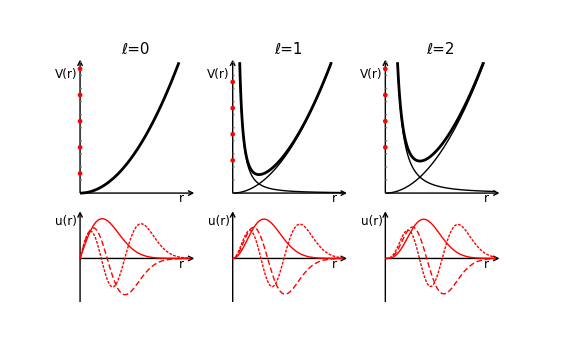

```mathematica
Figure[
{
With[
{
rMax=5,dr=0.1,
VMax=10,dV=0.1,
fMax=1,df=0.05
},
{
Multipanel[
{{0,1},{0,1}},
{2,3},
XPlotRanges->{0,rMax},
XGapSizes->0.15,
YPlotRanges->{{0,VMax},{-fMax,fMax}},
YPanelSizes->{1.5,1},
ShowPanelLetter->False,
Frame->False,
ExtendRange->0.1,
Margin->20
],

Table[
{
l=s-1,

(* top panel -- potential *)

FigurePanel[{1,s}],

(* column label *)
ScaledLabel[{0.5,1},Row[{"ℓ","=",l}],FontSize->15],

(* axes *)
SchemeAxis[
{Bottom,Left},
{{0,rMax+dr},{0,VMax+dV}},
LabB->textit["r"],LabL->Row[{textit[V],"(",textit["r"],")"}],
PosnB->0.9,PosnL->0.9,OrientationL->Horizontal,OffsetL->{1,0},BufferL->0.5,
Ticks->{None,LinTicks[0,VMax,1,1,ShowTickLabels->False,TickLengthScale->0.5]},
TickLineColor->Gray
],

(* potential plots *)
SchemeLine[Plot[VHO[l,r],{r,0,rMax},PlotRange->{0,VMax}],Thickness->2],
If[
l>0,
{
SchemeLine[Plot[VHO[0,r],{r,0,rMax},PlotRange->{0,VMax}]],
SchemeLine[Plot[VCent[l,r],{r,0,rMax},PlotRange->{0,VMax}],Dashing->3]
}
],

(* dots for energies *)
SetOptions[SchemeCircle,Color->Red],
Table[
SchemeCircle[{0,2*n+l+3/2},Point[2],Show->((2*n+l+3/2)<=VMax)],
{n,0,VMax}
],

(* bottom panel -- auxiliary radial wave function *)

FigurePanel[{2,s}],

(* axes *)
SchemeAxis[
{Bottom,Left},
{{0,rMax+dr},{-fMax,fMax+df}},
LabB->textit["r"],LabL->Row[{textit[u],"(",textit["r"],")"}],
PosnB->0.9,PosnL->0.9,OrientationL->Horizontal,OffsetL->{1,0},BufferL->0.5
],

(* wave function plots *)
Table[
SchemeLine[
Plot[u[n,l,r],{r,0,rMax},PlotRange->{-fMax,fMax}],
Color->Red,Dashing->Switch[n,0,None,1,4,2,2]
],
{n,0,2}
],

},
{s,1,3}
]

}
]
},
PlotRange->{{0,1},{0,1}},
ImageSize->72*{8,5}
]
```

## Attaching text labels to plots -- Woods-Saxon wave functions

In this example, we use LevelScheme to control the appearance of the plot line, by feeding the output of Plot to SchemeLine, which takes the plot's curve, extracts the coordinates of its points, and (re)draws the curve following these points, but using SchemeLine's formatting options.

Set up some automated label formatting functions

```mathematica
SpectroscopicLetter[0]="s";
SpectroscopicLetter[1]="p";
SpectroscopicLetter[2]="d";
SpectroscopicLetter[3]="f";
SpectroscopicLetter[4]="g";
SpectroscopicLetter[5]="h";
SpectroscopicLetter[6]="i";
SpectroscopicLetter[7]="j";
SpectroscopicLetter[8]="k";
ShellLabel[{n_,l_,j_}]:=Row[{n,Subscript[SpectroscopicLetter[l],SolidusFractionize[j]]}];
```

Define wave functions

```mathematica
g[b_,n_,l_,r_]:=Sqrt[2*Factorial[n]/(b^3*Gamma[n+l+3/2])]*(r/b)^l*Exp[-r^2/(2*b^2)]*LaguerreL[n,l+1/2,(r/b)^2];
```

```mathematica
b40=1.94;
R0s1[r_]:=0.995*g[b40,0,0,r]-0.087*g[b40,1,0,r]-0.034*g[b40,2,0,r];
R0p3[r_]:=0.998*g[b40,0,1,r]-0.044*g[b40,1,1,r]-0.026*g[b40,2,1,r];
R0p1[r_]:=0.999*g[b40,0,1,r]-0.002*g[b40,1,1,r]-0.009*g[b40,2,1,r];
R0s1HO[r_]:=g[b40,0,0,r];
R0p3HO[r_]:=g[b40,0,1,r];
R0p1HO[r_]:=g[b40,0,1,r];
```

Generate figure

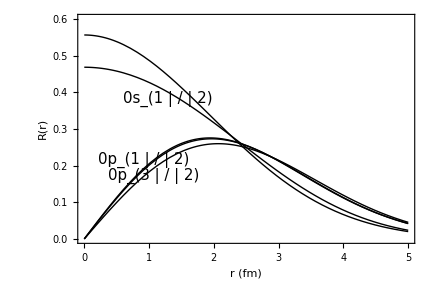

```mathematica
Figure[
{
SetOptions[SchemeLine,FontSize->15],
SchemeLine[
Plot[R0s1[r],{r,0,5}],
LabB->ShellLabel[{0,0,1/2}],PosnB->0.25
],
SchemeLine[
Plot[R0p3[r],{r,0,5}],
LabB->ShellLabel[{0,1,3/2}],PosnB->0.25
],
SchemeLine[
Plot[R0p1[r],{r,0,5}],
LabT->ShellLabel[{0,1,1/2}],PosnT->0.25,NudgeT->2
],

SetOptions[SchemeLine,Dashing->3],
SchemeLine[Plot[R0s1HO[r],{r,0,5}]],
SchemeLine[Plot[R0p3HO[r],{r,0,5}]],

},
PlotRange->{{0,5},{0,0.6}},
ImageSize->72*{6,4},
Frame->True,FrameTicks->Automatic,LabB->Row[{textit["r"]," (fm)"}],
LabL->Row[{textit["R"],"(",textit["r"],")"}],
FontSize->15,TickFontSize->12
]
```

## Contour plot superposed on chart, using online isotope data -- Chart of nuclides

This provides an example of constructing a table automatically.

Labels and shading of stable isotopes are produced automatically from data provided by Mathematica's IsotopeData function.
Requires network connection for access to Wolfram data.

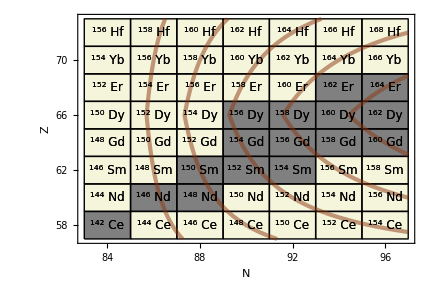

```mathematica
(* Define some functions useful for labeling the chart of the nuclides *)
IsStable[N_,Z_]:=IsotopeData[{Z,N+Z},"Stable"];
ChemicalSymbol[N_,Z_]:=IsotopeData[{Z,N+Z},"Symbol"];;

(* Make the contour plot *)
(* The option DisplayFunction->Identity prevents it from actually displaying here. *)
PFactor8250[N_,Z_]:=Module[
{Np,Nn},
Nn=Min[N-82,126-N];
Np=Min[Z-50,82-Z];

Np*Nn/(Np+Nn)
];
ZMin=58;
ZMax=72;
NMin=84;
NMax=96;
Figure[{

(* use variable name "NValue" instead of "N", since N is already used as a Mathematica function name, and ContourPlot therefore produces an error message *)
ExampleChartPlot=ContourPlot[PFactor8250[NValue,ZValue],{NValue,NMin-1,NMax+1},{ZValue,ZMin-1,ZMax+1},PlotPoints->100,ContourShading->False,Contours->Range[3,7],ContourStyle->{BurntSienna}];

(* draw contour line in layer "1.5" to go in front of boxes but behind layer white-out boxes,
but with opacity 0.5 so boxes show through *)
RawGraphics[
ExampleChartPlot, Color->BurntSienna, Layer->1.5,Thickness->3,Opacity->0.5
],

Table[
SchemeBox[
{{NValue-1,NValue+1},{ZValue-1,ZValue+1}},
LabC->ChemicalSymbol[NValue,ZValue],
FillColor->If[IsStable[NValue,ZValue],Gray,LightBeige],
BackgroundC->If[IsStable[NValue,ZValue],Gray,LightBeige]
],
{ZValue,ZMin,ZMax,2},{NValue,NMin,NMax,2}
]

},
PlotRange->{{NMin-1,NMax+1},{ZMin-1,ZMax+1}},ImageSize->72*{6,4},
LabB->textit["N"],LabL->textit["Z"],
FrameTicks->{LinTicks[NMin,NMax,2,1],LinTicks[ZMin,ZMax,2,1],{},{}},
Frame->True
]
```